This code is released under the GPL license. Copyright 2019 by C. Escamilla-Rivera (celia.escamillarivera@gmail.com)
Repository at: https://github.com/celia-escamilla-rivera/Cosmography_from_DEEoS
Cite “Unveiling the dark energy equation of state from cosmography” by Escamilla-Rivera C and S. Capozziello. [arXiv:1905.04602]

Calculations of cosmographic parameters from Dark Energy EoS

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Defining cosmography functions

```mathematica
q=(Subscript[Ω, m]*(1+z)^3+(1+3*w)*(1-Subscript[Ω, m])*(1+z)^(3*(1+w)))/(2*(Subscript[Ω, m]*(1+z)^3+(1-Subscript[Ω, m])*(1+z)^(3*(1+w))));
j=1+(9*w*(1+w)*(1-Subscript[Ω, m])*(1+z)^(3*(1+w)))/(2*(Subscript[Ω, m]*(1+z)^3+(1-Subscript[Ω, m])*(1+z)^(3*(1+w))));
```

### Cosmological w-models

#### Case w=0

```mathematica
w=0;
```

```mathematica
q
```

1/2

```mathematica
j
```

1

```mathematica
qdust=Plot[q,{z,0,2.2}, Frame-> True,FrameLabel-> {"z","q(z)"},PlotStyle-> {Darker[Gray],Dotted},LabelStyle->Directive[18],PlotRange->{{0,2.2},{-0.6,1}}]
```

-Graphics-

```mathematica
jdust=Plot[j,{z,0,2.2}, Frame-> True,FrameLabel-> {"z","j(z)"},PlotStyle-> {Darker[Gray],Dotted},LabelStyle->Directive[18]]
```

-Graphics-

```mathematica
Export["qdust.m",qdust];
Export["jdust.m",jdust];
```

#### Case LCDM: w=-1

```mathematica
w=-1;
```

```mathematica
q
```

(-2 (1-Ω_m)+(1+z)^3 Ω_m)/(2 (1-Ω_m+(1+z)^3 Ω_m))

```mathematica
j
```

1

```mathematica
Subscript[Ω, m]=0.315;
```

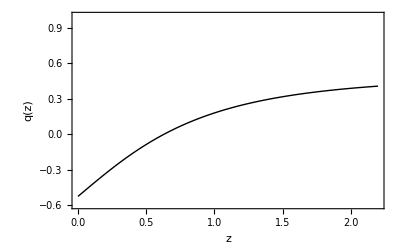

```mathematica
qlcdm=Plot[q,{z,0,2.2}, Frame-> True,Axes-> None,FrameLabel-> {"z","q(z)"},PlotStyle-> {Black,Thick},LabelStyle->Directive[18],PlotRange->{{0,2.2},{-0.6,1}}]
```

```mathematica
Export["qlcdm.m",qlcdm];
```

#### Case Ultra-relativistic matter: w=1/3

```mathematica
w=1/3;
```

```mathematica
q
```

(2 (1+z)^4 (1-Ω_m)+(1+z)^3 Ω_m)/(2 ((1+z)^4 (1-Ω_m)+(1+z)^3 Ω_m))

```mathematica
j
```

1+(2 (1+z)^4 (1-Ω_m))/((1+z)^4 (1-Ω_m)+(1+z)^3 Ω_m)

```mathematica
Subscript[Ω, m]=0.315;
```

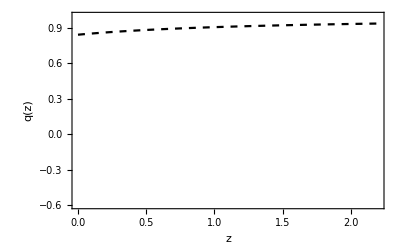

```mathematica
qult=Plot[q,{z,0,2.2}, Frame-> True,FrameLabel-> {"z","q(z)"},PlotStyle-> {Black,Dashed},LabelStyle->Directive[18],PlotRange->{{0,2.2},{-0.6,1}},Axes-> None]
```

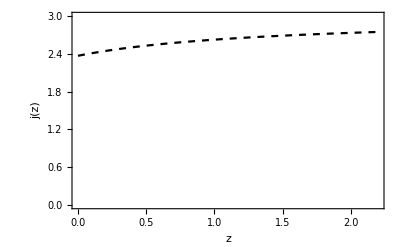

```mathematica
jult=Plot[j,{z,0,2.2}, Frame-> True,FrameLabel-> {"z","j(z)"},PlotStyle-> {Black,Dashed},LabelStyle->Directive[18],PlotRange->{{0,2.2},{0,3}}]
```

```mathematica
Export["qult.m",qult];
Export["jult.m",jult];
```

#### Case phantom energy: w<-1

```mathematica
w=-3;
```

```mathematica
q
```

(-(8 (1-Ω_m))/(1+z)^6+(1+z)^3 Ω_m)/(2 ((1-Ω_m)/(1+z)^6+(1+z)^3 Ω_m))

```mathematica
j
```

1+(27 (1-Ω_m))/((1+z)^6 ((1-Ω_m)/(1+z)^6+(1+z)^3 Ω_m))

```mathematica
Subscript[Ω, m]=0.315;
```

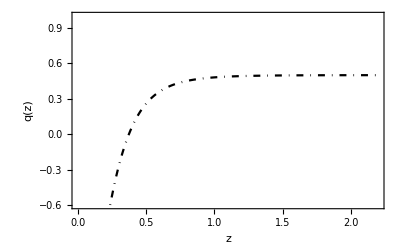

```mathematica
qphan=Plot[q,{z,0,2.2}, Axes-> None,Frame-> True,FrameLabel-> {"z","q(z)"},PlotStyle-> {Black,DotDashed},LabelStyle->Directive[18],PlotRange->{{0,2.2},{-0.6,1}}]
```

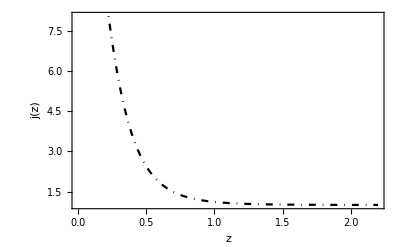

```mathematica
jphan=Plot[j,{z,0,2.2}, Frame-> True,FrameLabel-> {"z","j(z)"},PlotStyle-> {Black,DotDashed},LabelStyle->Directive[18]]
```

```mathematica
Export["qphan.m",qphan];
Export["jphan.m",jphan];
```